```mathematica
(*Off[SixJSymbol::tri];
Off[ThreeJSymbol::tri];
Off[ClebschGordan::tri];
Off[ClebschGordan::phy];
$Assumptions=α∈Reals;*)
```

```mathematica
(*ColorData[63,"ColorList"]*)
ColorPalette={-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
(* The total angular momentum magnetic quantum number is conserved, so we solve only for a specific Jz *)
Jz=1;
(* The full two-body energy cutoff for the basis *)
EMax=18;(*=NMax+3*)
(* Easiest to set a value of a at the beginning so that the matrix elements become numerical *)
a=-1;
(* This is needed because the eigenvalue solver finds the eigenvalues with the smallest magnitude. Choose a postive number at least the size of the most negative eigenvalue expected *)
EOffset=10;
```

```mathematica
(* Determine the two body l=0 center of mass eigenenergies in the absence of SOC from Busch formula *)
If[a!=0&&a≠∞&&a≠-∞,
νValues=Table[FindRoot[Sqrt[2]Gamma[-ν]/Gamma[-ν-1/2]==1/a,{ν,νGuess},AccuracyGoal->25],{νGuess,-4,(EMax/2-1.5)+.25,.01*Sqrt[2]}];
νValues=DeleteDuplicates[νValues,Abs[ReplaceAll[ν,#1]-ReplaceAll[ν,#2]]<=.1&];,
If[a==0,νValues=Table[{ν->i},{i,0,EMax-3}] (* Handle a=0 case *),
νValues=Table[{ν->i-1/2},{i,0,EMax-3.5}];(*Handle a=+-∞ case *)]
]

EValues=Sort[2ν+3/2/.νValues] ;(* List of l=0 energies under the cutoff *)
νValues=Sort[Flatten[ν/.νValues]];
```

```mathematica
(* Make sure all Busch energies are below the cutoff *)
While[2*νValues[[-1]]+3>EMax,νValues=Delete[νValues,-1]]
While[EValues[[-1]]+3/2>EMax,EValues=Delete[EValues,-1]]
```

```mathematica
(* List of Busch quantum numbers under the energy cutoff *)
νValues
```

{-0.256299,0.669483,1.63632,2.61694,3.60392,4.59444,5.58713,6.58129}

```mathematica
(* List of Busch 2-body CoM Energies below the cutoff *)
EValues
```

{0.987402,2.83897,4.77264,6.73387,8.70785,10.6889,12.6743,14.6626}

```mathematica
(* Indexing of states *)
Clear[ni,li,Ni,Li,si,ji,Ji];imax=0;i=0;
verbose=False;

(* Function to print quantum numbers of state i if needed *)
PrintState[i_]:=Print["|",i,">=|",ni[i],"(",li[i],si[i],")",ji[i],";",Ni[i],Li[i],";(",ji[i],Li[i],")",Ji[i],Jzi[i]">"];

(* When the lowest Busch energy is less than 3/2, we can get higher N in each shell *)
If[EValues[[1]]≤3/2,δEMax=EValues[[1]]-3/2,δEMax=0]; 

For[EShell=3,EShell≤EMax,++EShell,
For[N0=0,2N0+3+δEMax≤EShell,++N0,
For[L=0,2 N0+L+3+δEMax≤EShell,++L,
For[s=0,s≤1,++s,
For[l=0,l==0||l<=EShell-2N0-L-3,++l,
For[j=Abs[l-s],j≤l+s,++j,
For[J=Max[Abs[j-L],Abs[Jz]],J≤j+L,J++,
If[l==0&&s==0,
For[ii=1,ii≤Length[EValues],++ii,
If[2N0+L+3/2+EValues[[ii]]>EShell,Break];
If[(EShell-1<2N0+L+3/2+EValues[[ii]]||EShell==3)&&2N0+L+3/2+EValues[[ii]]≤EShell,
++i;++imax;
Ji[i]=J;
Jzi[i]=Jz;
Ni[i]=N0;
Li[i]=L;
si[i]=s;
li[i]=l;
ji[i]=j;
ni[i]=νValues[[ii]];
If[verbose,
Print["E_shell=",EShell,"   |",i,">=|",ni[i],"(",l,s,")",j,";",N0,L,";(",j,L,")",J," ",Jz,">"];
Print["E=",2N0+L+3/2+2*ni[i]+3/2];](* End If[Verbose] *)
](* End If[EvenQ... ] *)
](* End ii loop *)(* End l==0 case, ν loop*),
For[n=0,2n+l+3/2+2N0+L+3/2≤EShell,++n,
If[EvenQ[l+s]&&2(N0+n)+L+l+3==EShell,
++i;++imax;
Ji[i]=J;
Jzi[i]=Jz;
Ni[i]=N0;
Li[i]=L;
si[i]=s;
li[i]=l;
ji[i]=j;
ni[i]=n;
If[verbose,
Print["E_shell=",EShell,"   |",i,">=|",ni[i],"(",l,s,")",j,";",N0,L,";(",j,L,")",J,Jz,">"];
Print["E=",2N0+L+3/2+2ni[i]+l+3/2];](* End If[Verbose] *)
] (* End If[EvenQ...] *)
](* End For[n=0...] *)
] (* End If[l==0] *)
] (* End J loop *)
] (* End j loop *)
](* End l loop *)
] (* End s loop *)
] (* End L loop *)
];(* End N0 loop *)
iShell[EShell]=imax;
] (* End EShell loop *)
Clear[i,ii,l,L,N0,n,s,j,J];
Print["There are a total of ",imax," ","included states."]
```

There are a total of 8592 included states.

```mathematica
(*shellSizeTableRashba=Table[{EShell,iShell[EShell]},{EShell,4,32,1}]
ListPlot[shellSizeTableRashba,Joined->True,PlotRange->{{0,32},{0,120000}},Axes->False,Frame->True,PlotLabel->"Number of states with E<=E_Max",FrameLabel->{"E_Max","Number of States"}];
ListPlot[{shellSizeTableRashba,shellSizeTableWeyl},Joined->True,PlotRange->{{0,32},{0,15000}},Axes->False,Frame->True,PlotLabel->"Number of states with E<=E_Max",FrameLabel->{"E_Max","Number of States"},PlotLegends->{"Rashba","Weyl"}]*)
```

```mathematica
(* Save all the angular momentum coupling coefficients after computing once *)
JThree[{j1_,j1m_},{j2_,j2m_},{J_,Jm_}]:=JThree[{j1,j1m},{j2,j2m},{J,Jm}]=ThreeJSymbol[{j1,j1m},{j2,j2m},{J,Jm}];
JSix[{j1_,j2_,j3_},{j4_,j5_,j6_}]:=JSix[{j1,j2,j3},{j4,j5,j6}]=SixJSymbol[{j1,j2,j3},{j4,j5,j6}];
(* 9-j symbol ({{j1, j2, j12}, {j3, j4, j34}, {j13, j24, j}})*)
JNine[{j1_,j2_,j12_},{j3_,j4_,j34_},{j13_,j24_,j_}]:=JNine[{j1,j2,j12},{j3,j4,j34},{j13,j24,j}]=Sum[(-1)^(2g)(2g+1)JSix[{j1,j2,j12},{j34,j,g}]JSix[{j3,j4,j34},{j2,g,j24}]JSix[{j13,j24,j},{g,j1,j3}],{g,Max[Abs[j1-j],Abs[j2-j34],Abs[j3-j24]],Min[j1+j,j2+j34,j3+j24],1-Mod[2*(j1+j),2]/2}]
```

```mathematica
(* Normalization factor for Busch wave functions. Provide a limiting definition for half-integer ν when a->+∞,-∞ *)
Clear[A];
AbsoluteTiming[If[a≠∞&&a≠-∞,A[ν_]:=A[ν]=((Gamma[-ν] (-PolyGamma[0,-1/2-ν]+PolyGamma[0,-ν]))/(8 π^2 Gamma[-1/2-ν]))^(-1/2),
For[ν0=-1/2,ν0<=νValues[[-1]]+.01,ν0++,A[N[ν0]]=N[Limit[((Gamma[-ν] (-PolyGamma[0,-1/2-ν]+PolyGamma[0,-ν]))/(8 π^2 Gamma[-1/2-ν]))^(-1/2),ν->ν0]]]
] (* End if *)
](* End AbsoluteTiming *)
```

{0.00004,Null}

```mathematica
(* This is the actual reduced matrix element of Q *)
Q[n1_,l1_,n_,l_]:=Q[n1,l1,n,l]= If[Abs[l1-l]==1,(I (-1)^(l1+1))/JThree[{l1,0},{1,0},{l,0}] √(n!n1!Gamma[n+l+3/2]Gamma[n1+l1+3/2])Sum[(-1)^(m+m1)/(m!m1!(n-m)!(n1-m1)!Gamma[m+l+3/2]Gamma[m1+l1+3/2])Which[l1==l+1,(l+1)/Sqrt[(2l+1)(2l+3)] (2m Gamma[m+m1+1+(l+l1)/2]-Gamma[m+m1+2+(l+l1)/2]),l1==l-1,l/Sqrt[(2l+1)(2l-1)]((2m+2l+1) Gamma[m+m1+1+(l+l1)/2]-Gamma[m+m1+2+(l+l1)/2]),True,0],{m,0,n},{m1,0,n1}],0];
(* This is the actual reduced matrix element of q, accounting for the Busch states at l=0 *)
q[n1_,l1_,n_,l_]:=q[n1,l1,n,l]=
If[l1==0&&l==1&&a≠0,Conjugate[q[n,1,n1,0]], (* Recursive definition for < ν l1=0 ||q || n l=1 > case *)
If[l1==1&&l==0&&a≠0, (* Definition for < n1 l1=1 ||q || ν l=0 > case *)
-I A[N[n]]Sqrt[Gamma[n1+5/2]/(2 π^3 Gamma[n1+1])](-1-2 n1+2 n)/(2 (n1-n) (1+n1-n)),
(* Case where neither l or l1=0 *)
Q[n1,l1,n,l]]];
```

```mathematica
(* Matrix elements of σ.q *)
(* Note that α is not included! *)
σq[n1_,s1_,l1_,j1_,L1_,J1_,J1z_,n_,s_,l_,j_,L_,J_,Jz_]:=  I 6. Sqrt[(2J+1)(2J1+1)(2j+1)(2j1+1)](-1)^(J+J1-J1z+j1+L+1)JThree[{J1,-J1z},{1,0},{J,Jz}]JSix[{j1,J1,L},{J,j,1}]JNine[{l1,l,1},{s1,s,1},{j1,j,1}]q[n1,l1,n,l](s1-s)
```

```mathematica
(* Matrix elements of Σ.Q *)
(* Note that α is not included! *)
ΣQ[l1_,s1_,j1_,N1_,L1_,J1_,J1z_,l_,s_,j_,N_,L_,J_,Jz_]:=
 I 6.Sqrt[2]Sqrt[(2j+1)(2j1+1)(2J+1)(2J1+1)](-1)^(J+J1-J1z+l)JThree[{J1,-J1z},{1,0},{J,Jz}]Q[N1,L1,N,L]Sum[(-1)^J2(2J2+1.)(2J21+1.)JSix[{l,1,j},{L,J,J2}]JSix[{l1,1,j1},{L1,J1,J21}]JSix[{J21,J1,l},{J,J2,1}]JNine[{L1,L,1},{s1,s,1},{J21,J2,1}],{J2,Abs[L-s],Abs[L+s]},{J21,Abs[L1-s1],Abs[L1+s1]}](KroneckerDelta[s,1]KroneckerDelta[s1,1])
```

```mathematica
(* Matrix σ.q+Σ.Q, stored as SparseArray *)
Print["There are a total of ",imax," ","included states."]
t=AbsoluteTime[];
σqΣQ=SparseArray[
Flatten[
ParallelTable[Quiet[If[Jzi[i]==Jzi[j]&&Abs[Ji[i]-1]≤Ji[j]≤Ji[i]+1,
If[Ni[i]==Ni[j]&&Li[i]==Li[j]&&Abs[li[i]-li[j]]==1&&Abs[si[i]-si[j]]==1&&Abs[ji[i]-1]≤ji[j]≤ji[i]+1,{{i,j}->Chop[σq[ni[i],si[i],li[i],ji[i],Li[i],Ji[i],Jzi[i],ni[j],si[j],li[j],ji[j],Li[j],Ji[j],Jzi[j]]]},(*ELSE*)If[ni[i]==ni[j]&&li[i]==li[j]&&si[i]==1&&si[j]==1&&Abs[Li[i]-Li[j]]==1,{{i,j}->Chop[ΣQ[li[i],si[i],ji[i],Ni[i],Li[i],Ji[i],Jzi[i],li[j],si[j],ji[j],Ni[j],Li[j],Ji[j],Jzi[j]]]},##&[]]
,##&[]](* If σq≠0 *)
,##&[]](* If ΔJ≤1 && Jz==Jz *)
](* End quiet *)
,{i,2,imax},{j,1,i-1}]
],{imax,imax}
];
σqΣQ=SparseArray[σqΣQ+ConjugateTranspose[σqΣQ]];
AbsoluteTime[]-t
```

There are a total of 8592 included states.

402.914692

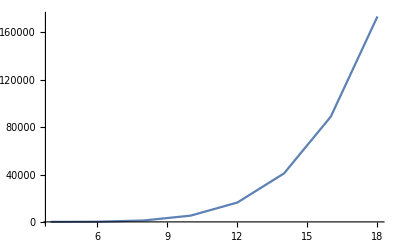

```mathematica
(* Plot the number of nonzero matrix elements *)
shellMETableRashba=Table[{EShell,Length@σqΣQ[[1;;iShell[EShell],1;;iShell[EShell]]]["NonzeroPositions"]},{EShell,4,Min[EMax,32],2}];
ListPlot[shellMETableRashba,Joined->True]
```

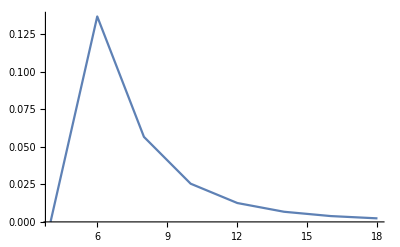

```mathematica
(* Plot the percentage of nonzero matrix elements to indicate sparsity *)
shellMEDensityTableRashba=Table[{EShell,Length@σqΣQ[[1;;iShell[EShell],1;;iShell[EShell]]]["NonzeroPositions"]/(iShell[EShell])^2},{EShell,4,Min[EMax,32],2}];
ListPlot[shellMEDensityTableRashba,Joined->True]
```

```mathematica
(* Matrix of Subscript[H, HO]+Subscript[H, contact], stored as SparseArray *)
H0=SparseArray[ParallelTable[{i,i}->2ni[i]+2Ni[i]+li[i]+Li[i]+3+EOffset,{i,1,imax}]];
```

```mathematica
Clear[Data]
αMin=0;αMax=0.5*Sqrt[3/2];αStep=N[1/200]*Sqrt[2];
nEigValues=20;
AbsoluteTiming[Do[Energies[α0]=Sort[Eigenvalues[SparseArray[H0+α0 σqΣQ],-nEigValues]],{α0,αMin,αMax,αStep}]]
Data[j_]:=Table[{α,Energies[α][[j]]-EOffset},{α,αMin,αMax,αStep}];
```

{1022.61838,Null}

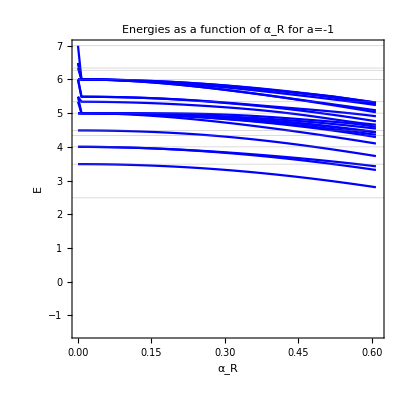

```mathematica
(* Plot of energies as a function of Subscript[α, Rashba] *)
ListPlot[Table[Data[i],{i,1,nEigValues}],Joined->True,PlotRange->{{αMin,αMax},{-1.5,7}},Frame->True,FrameLabel->{"α_R","E"},PlotStyle->Directive[Blue],GridLines->{{},Join[EValues+3/2,EValues+5/2,EValues+7/2,Table[i+3,{i,1,EMax-4}]]},AspectRatio->1.0,PlotLabel->StringJoin["Energies as a function of α_R for a=",ToString[a]]]
```

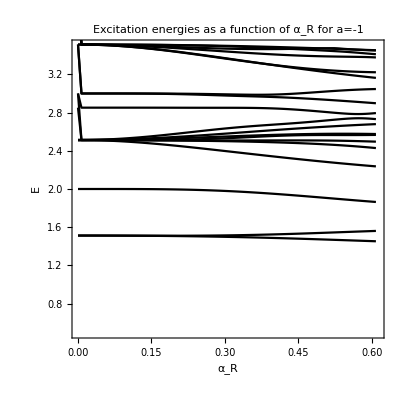

```mathematica
(* Plot of excitation energies as a function of Subscript[α, Rashba] *)
(* If you want to do for Jz≠0, need to run Jz=0 first to determine GS energy *)
If[Jz==0,EGS[a]=Table[Energies[α][[1]],{α,αMin,αMax,αStep}]];
DataExcitation[j_]:=Table[{α,Energies[α][[j]]-EGS[a][[Round[α/αStep]+1]]},{α,αMin,αMax,αStep}]
If[a==∞,plotMin=0.5;plotMax=3.5];
If[a==1,plotMin=0.5;plotMax=4.5];
If[a==0,plotMin=0.5;plotMax=3.5];
If[a==-1,plotMin=0.5;plotMax=3.5];
Fig=ListPlot[Table[DataExcitation[i],{i,2,nEigValues}],Joined->True,PlotRange->{{αMin,αMax},{plotMin,plotMax}},Frame->True,FrameLabel->{"α_R","E"},PlotStyle->Directive[Black],AspectRatio->1.0,PlotLabel->StringJoin["Excitation energies as a function of α_R for a=",ToString[a]]]
If[Jz==0,If[a==∞,Export["/Users/cdschillaci/Desktop/Paper with Tom/Mathematica/Figures/RashbaExcitationaInf.eps",Fig]];
If[a==1,Export["/Users/cdschillaci/Desktop/Paper with Tom/Mathematica/Figures/RashbaExcitationa1.eps",Fig]];
If[a==0,Export["/Users/cdschillaci/Desktop/Paper with Tom/Mathematica/Figures/RashbaExcitationa0.eps",Fig]];
If[a==-1,Export["/Users/cdschillaci/Desktop/Paper with Tom/Mathematica/Figures/RashbaExcitationa-1.eps",Fig]];]
```

```mathematica
(* Define convergence as absolute convergence. I like incrementing shells by 2 to increase the CM excitations for Busch energies evenly *)
conv[Convergence_]:=Abs[(Convergence[[-1,2]]-Convergence[[-3,2]])];
```

```mathematica
(* Create lists of eigenvalues for different EMax *)
Clear[i];
αTest=0.5;
Convergence1={};Convergence2={};Convergence3={};Convergence4={};
Convergence5={};Convergence6={};Convergence7={};Convergence8={};
FullH=H0+αTest σqΣQ;
For[Emax=6,Emax≤EMax,Emax+=2,
H=Chop[N[SparseArray[FullH[[1;;iShell[Emax],1;;iShell[Emax]]]]]];
EList=Eigenvalues[H,-8]-EOffset;
AppendTo[Convergence1,{Emax,EList[[-1]]}];AppendTo[Convergence2,{Emax,EList[[-2]]}];
AppendTo[Convergence3,{Emax,EList[[-3]]}];AppendTo[Convergence4,{Emax,EList[[-4]]}];
AppendTo[Convergence5,{Emax,EList[[-5]]}];AppendTo[Convergence6,{Emax,EList[[-6]]}];
AppendTo[Convergence7,{Emax,EList[[-7]]}];AppendTo[Convergence8,{Emax,EList[[-8]]}];]
```

```mathematica
(* Absolute convergence of eigenvalues at EMax compared to EMax-2 *)
conv[Convergence1]
conv[Convergence2]
conv[Convergence3]
conv[Convergence4]
conv[Convergence5]
conv[Convergence6]
conv[Convergence7]
conv[Convergence8]
```

0.00749484

1.8936×10^-12

0.000879294

0.00713641

3.17399×10^-11

0.0031867

0.000709703

0.00574748

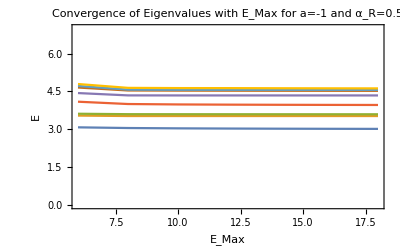

```mathematica
(* Make convergence plots *)
ListPlot[{Convergence1,Convergence2,Convergence3,Convergence4,Convergence5,Convergence6,Convergence7,Convergence8},Joined->True,Axes->False,Frame->True,PlotRange->{{6,EMax},{0,7}},PlotLabel->StringJoin["Convergence of Eigenvalues with E_Max for a=", ToString[a]," and α_R=",ToString[αTest]],FrameLabel->{"E_Max","E"}]
```

```mathematica
(* Create lists of eigenvalues for different EMax *)
Clear[i];
αTest=αMax;
Convergence1={};Convergence2={};Convergence3={};Convergence4={};
Convergence5={};Convergence6={};Convergence7={};Convergence8={};
FullH=H0+αTest σqΣQ;
For[Emax=6,Emax≤EMax,Emax+=2,
H=Chop[N[SparseArray[FullH[[1;;iShell[Emax],1;;iShell[Emax]]]]]];
EList=Eigenvalues[H,-8]-EOffset;
AppendTo[Convergence1,{Emax,EList[[-1]]}];AppendTo[Convergence2,{Emax,EList[[-2]]}];
AppendTo[Convergence3,{Emax,EList[[-3]]}];AppendTo[Convergence4,{Emax,EList[[-4]]}];
AppendTo[Convergence5,{Emax,EList[[-5]]}];AppendTo[Convergence6,{Emax,EList[[-6]]}];
AppendTo[Convergence7,{Emax,EList[[-7]]}];AppendTo[Convergence8,{Emax,EList[[-8]]}];]
```

```mathematica
(* Absolute convergence of eigenvalues at EMax compared to EMax-2 *)
conv[Convergence1]
conv[Convergence2]
conv[Convergence3]
conv[Convergence4]
conv[Convergence5]
conv[Convergence6]
conv[Convergence7]
conv[Convergence8]
```

0.0122234

1.10674×10^-10

0.00233779

0.0115447

1.0633×10^-9

0.0103058

0.00255556

0.006795

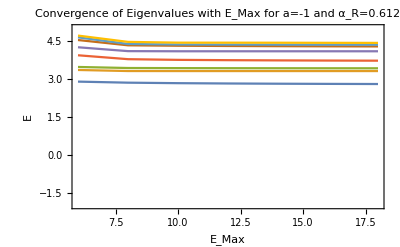

```mathematica
(* Make convergence plots *)
ListPlot[{Convergence1,Convergence2,Convergence3,Convergence4,Convergence5,Convergence6,Convergence7,Convergence8},Joined->True,Axes->False,Frame->True,PlotRange->{{6,EMax},{-2,5}},PlotLabel->StringJoin["Convergence of Eigenvalues with E_Max for a=", ToString[a]," and α_R=",ToString[αTest]],FrameLabel->{"E_Max","E"}]
```

```mathematica
(* Save Data for plotting together later *)
If[Jz==0,If[a==0,Data0R=Table[Data[i],{i,1,nEigValues,1}];DataExcitation0R=Table[DataExcitation[i],{i,2,nEigValues}]];
If[a==-1,Datam1R=Table[Data[i],{i,1,nEigValues,1}];DataExcitationm1R=Table[DataExcitation[i],{i,2,nEigValues}]];
If[a==1,Datap1R=Table[Data[i],{i,1,nEigValues,1}];DataExcitationp1R=Table[DataExcitation[i],{i,2,nEigValues}]];
If[a==∞,DataInfR=Table[Data[i],{i,1,nEigValues,1}];DataExcitationInfR=Table[DataExcitation[i],{i,2,nEigValues}]];]

If[Jz==1,If[a==0,Data0RJz1=Table[Data[i],{i,1,nEigValues,1}];DataExcitation0RJz1=Table[DataExcitation[i]+Data0RJz1[[1,1]]-Data0R,{i,2,nEigValues}]];
If[a==-1,Datam1RJz1=Table[Data[i],{i,1,nEigValues,1}];DataExcitationm1RJz1=Table[DataExcitation[i],{i,2,nEigValues}]];
If[a==1,Datap1RJz1=Table[Data[i],{i,1,nEigValues,1}];DataExcitationp1RJz1=Table[DataExcitation[i],{i,2,nEigValues}]];
If[a==∞,DataInfRJz1=Table[Data[i],{i,1,nEigValues,1}];DataExcitationInfRJz1=Table[DataExcitation[i],{i,2,nEigValues}]];]
```

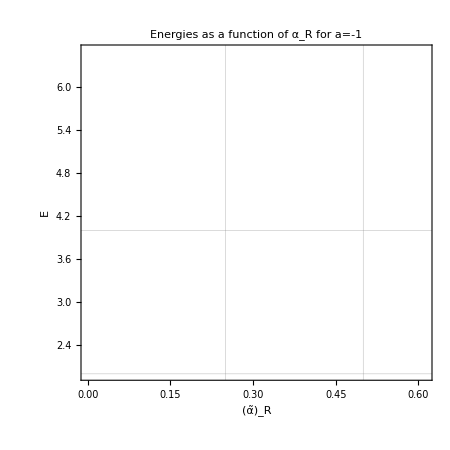

```mathematica
ListPlot[Table[Data0R[[i]],{i,1,nEigValues,1}],PlotStyle->Directive[Black,Thick],Joined->True,Frame->True,GridLines->{{.25,.5},{2,4}},PlotRange->{{0,αMax},{2,6.5}},ImageSize->450,FrameLabel->{Text[Style[ToExpression["\\tilde{\\alpha}_R",TeXForm,HoldForm],20]],Text[Style[ToExpression["energy",TeXForm,HoldForm],20]]},LabelStyle->14,AspectRatio->1.0,PlotLabel->StringJoin["Energies as a function of α_R for a=",ToString[a]]]
```

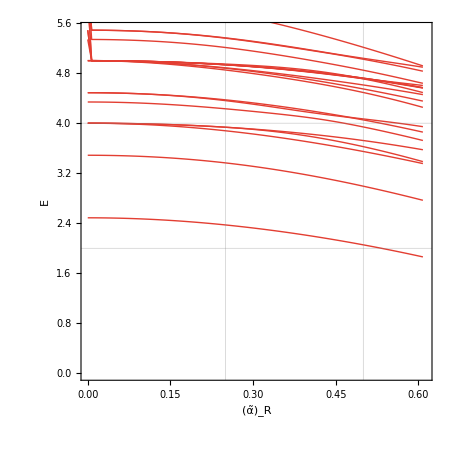

```mathematica
Format[energy,TraditionalForm]:="E"
Fig=Show[
ListPlot[Table[Data0R[[i]],{i,1,nEigValues,1}],PlotStyle->Directive[Black,Thick],Joined->True,Frame->True,GridLines->{{.25,.5},{2,4}},PlotRange->{{0,αMax},{0,5.5}},ImageSize->450,FrameLabel->{Text[Style[ToExpression["\\tilde{\\alpha}_R",TeXForm,HoldForm],20]],Text[Style[ToExpression["energy",TeXForm,HoldForm],20]]},LabelStyle->14,AspectRatio->1.0],
(**)
ListPlot[Table[Datam1R[[i]],{i,1,nEigValues,1}],Joined->True,PlotStyle->Directive[ColorPalette[[1]],Thick]
]
]
(*Export["/Users/cdschillaci/Desktop/Paper with Tom/Mathematica/Figures/Rashbaa0am1.eps",Fig]*)
```

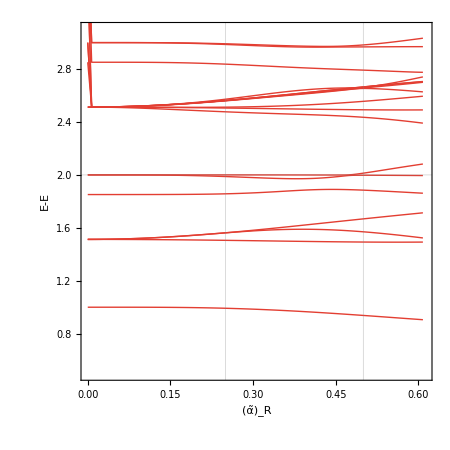

/Users/cdschillaci/Desktop/Paper with Tom/Mathematica/Figures/RashbaExcitation_a0am1.eps

```mathematica
Format[energy,TraditionalForm]:="E"
Fig=Show[
ListPlot[Table[DataExcitation0R[[i]],{i,1,nEigValues-1,1}],PlotStyle->Directive[Black,Thick],Joined->True,Frame->True,GridLines->{{.25,.5},{2,4}},PlotRange->{{0,αMax},{0.5,3.1}},ImageSize->450,FrameLabel->{Text[Style[ToExpression["\\tilde{\\alpha}_R",TeXForm,HoldForm],20]],Text[Style[ToExpression["energy-energy_GS",TeXForm,HoldForm],20]]},LabelStyle->14,AspectRatio->1.0],
(**)
ListPlot[Table[DataExcitationm1R[[i]],{i,1,nEigValues-2,1}],Joined->True,PlotStyle->Directive[ColorPalette[[1]],Thick]
]
]
Export["/Users/cdschillaci/Desktop/Paper with Tom/Mathematica/Figures/RashbaExcitation_a0am1.eps",Fig]
```

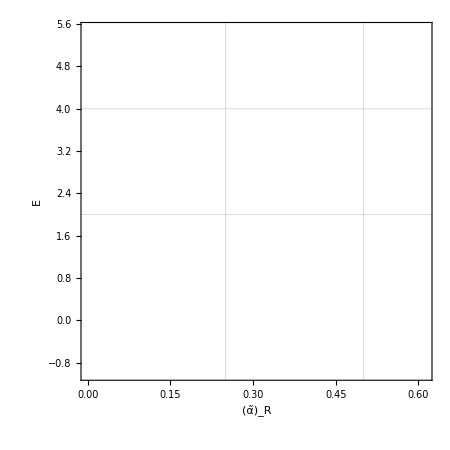

```mathematica
Format[energy,TraditionalForm]:="E"
Fig=Show[
ListPlot[Table[Datap1R[[i]],{i,1,nEigValues,1}],PlotStyle->Directive[ColorPalette[[1]],Thick],Joined->True,Frame->True,GridLines->{{.25,.5},{2,4}},PlotRange->{{0,αMax},{-1,5.5}},ImageSize->450,FrameLabel->{Text[Style[ToExpression["\\tilde{\\alpha}_R",TeXForm,HoldForm],20]],Text[Style[ToExpression["energy",TeXForm,HoldForm],20]]},LabelStyle->14,AspectRatio->1.0],
(**)
ListPlot[Table[DataInfR[[i]],{i,1,nEigValues,1}],Joined->True,PlotStyle->Directive[Black,Thick]
]
]
(*Export["/Users/cdschillaci/Desktop/Paper with Tom/Mathematica/Figures/Rashbaa1aInf.eps",Fig]*)
```

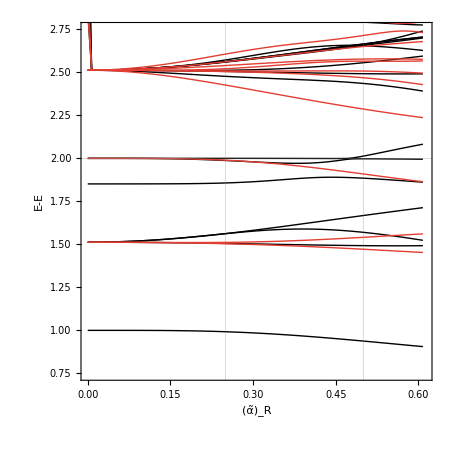

/Users/cdschillaci/Desktop/Paper with Tom/Mathematica/Figures/RashbaExcitation_am1Jz0Jz1.eps

```mathematica
Format[energy,TraditionalForm]:="E"
Fig=Show[
ListPlot[Table[DataExcitationm1R[[i]],{i,1,nEigValues-1,1}],PlotStyle->Directive[Black,Thick],Joined->True,Frame->True,GridLines->{{.25,.5},{2,4}},PlotRange->{{0,αMax},{0.75,2.75}},ImageSize->450,FrameLabel->{Text[Style[ToExpression["\\tilde{\\alpha}_R",TeXForm,HoldForm],20]],Text[Style[ToExpression["energy-energy_GS",TeXForm,HoldForm],20]]},LabelStyle->14,AspectRatio->1.0],
(**)
ListPlot[Table[DataExcitationm1RJz1[[i]],{i,1,nEigValues-2,1}],Joined->True,PlotStyle->Directive[ColorPalette[[1]],Thick]
]
]
Export["/Users/cdschillaci/Desktop/Paper with Tom/Mathematica/Figures/RashbaExcitation_am1Jz0Jz1.eps",Fig]
```

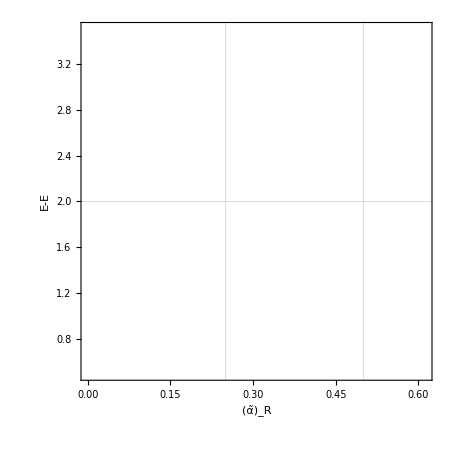

/Users/cdschillaci/Desktop/Paper with Tom/Mathematica/Figures/RashbaExcitation_aInfJz0Jz1.eps

```mathematica
Format[energy,TraditionalForm]:="E"
Fig=Show[
ListPlot[Table[DataExcitationInfR[[i]],{i,1,nEigValues-1,1}],PlotStyle->Directive[Black,Thick],Joined->True,Frame->True,GridLines->{{.25,.5},{2,4}},PlotRange->{{0,αMax},{0.5,3.5}},ImageSize->450,FrameLabel->{Text[Style[ToExpression["\\tilde{\\alpha}_R",TeXForm,HoldForm],20]],Text[Style[ToExpression["energy-energy_GS",TeXForm,HoldForm],20]]},LabelStyle->14,AspectRatio->1.0],
(**)
ListPlot[Table[DataExcitationInfRJz1[[i]],{i,1,nEigValues-2,1}],Joined->True,PlotStyle->Directive[ColorPalette[[1]],Thick]
]
]
Export["/Users/cdschillaci/Desktop/Paper with Tom/Mathematica/Figures/RashbaExcitation_aInfJz0Jz1.eps",Fig]
```

```mathematica
(* Comparison plot with Yin, Gopalakrishnan, Blume *)
αMax2=0.75;αStep2=αStep;
nEigValues2=10;
AbsoluteTiming[Do[Energies2[α0]=Sort[Eigenvalues[SparseArray[H0+α0 σqΣQ],-nEigValues2]],{α0,0,αMax2,αStep}]]
Data2[j_]:=Table[{α,Energies2[α][[j]]-EOffset},{α,0,αMax2,αStep2}];
```

{6460.16507,Null}

```mathematica
If[a==1,
Datap1R2=Join[{Data2[1]},{Data2[3]},{Data2[5]}(*,{Data2[6]},{Data2[7]},{Data2[8]}*)];
Fig=Show[
ListPlot[Datap1R2,PlotStyle->Directive[Black,Thick],Joined->True,Frame->True,GridLines->{{.25,.5},{2,4}},PlotRange->{{0,αMax2},{0,4}},ImageSize->450,FrameLabel->{Text[Style[ToExpression["\\tilde{\\alpha}_R",TeXForm,HoldForm],20]],Text[Style[ToExpression["energy",TeXForm,HoldForm],20]]},LabelStyle->14,AspectRatio->0.75],
(**)
Plot[{EValues[[1]]+3/2-2 α^2,EValues[[1]]+7/2-2 α^2,EValues[[2]]+3/2-2 α^2},{α,0,αMax2},PlotStyle->Directive[Red,Thick]]
];(* end Show *)
Print[Fig];
Export["/Users/cdschillaci/Desktop/Paper with Tom/Mathematica/Figures/ComparisonWithPertap1.eps",Fig];
]
```

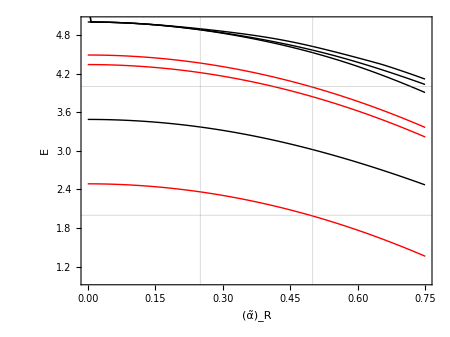

```mathematica
If[a==-1,
Datam1R2=Join[{Data2[1]},{Data2[6]},{Data2[7]},{Data2[8]}(*,{Data2[6]},{Data2[7]},{Data2[8]}*)];
Fig=Show[
ListPlot[Datam1R2,PlotStyle->Directive[Black,Thick],Joined->True,Frame->True,GridLines->{{.25,.5},{2,4}},PlotRange->{{0,αMax2},{1,5}},ImageSize->450,FrameLabel->{Text[Style[ToExpression["\\tilde{\\alpha}_R",TeXForm,HoldForm],20]],Text[Style[ToExpression["energy",TeXForm,HoldForm],20]]},LabelStyle->14,AspectRatio->0.75],
(**)
Plot[{EValues[[1]]+3/2-2 α^2,EValues[[1]]+7/2-2 α^2,EValues[[2]]+3/2-2 α^2},{α,0,αMax2},PlotStyle->Directive[Red,Thick]]
];(* end Show *)
Print[Fig];
Export["/Users/cdschillaci/Desktop/Paper with Tom/Mathematica/Figures/ComparisonWithPertam1.eps",Fig];
]
```

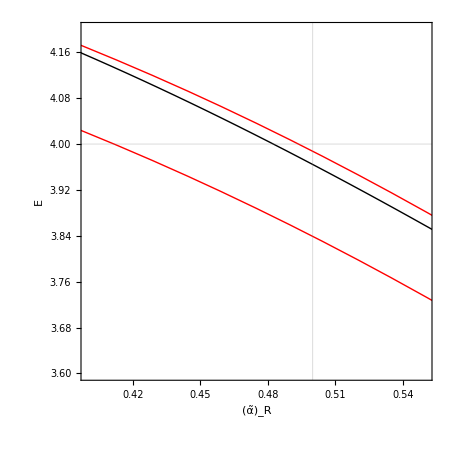

```mathematica
If[a==-1,
Datam1R2=Join[{Data2[4]},{Data2[5]},{Data2[6]},{Data2[7]}(*,{Data2[6]},{Data2[7]},{Data2[8]}*)];
Fig=Show[
ListPlot[Datam1R2,PlotStyle->Directive[Black,Thick],Joined->True,Frame->True,GridLines->{{.25,.5},{2,4}},PlotRange->{{.4,.55},{3.6,4.2}},ImageSize->450,FrameLabel->{Text[Style[ToExpression["\\tilde{\\alpha}_R",TeXForm,HoldForm],20]],Text[Style[ToExpression["energy",TeXForm,HoldForm],20]]},LabelStyle->14,AspectRatio->1],
(**)
Plot[{EValues[[1]]+3/2-2 α^2,EValues[[1]]+7/2-2 α^2,EValues[[2]]+3/2-2 α^2},{α,0,αMax2},PlotStyle->Directive[Red,Thick]]
];(* end Show *)
Print[Fig];
Export["/Users/cdschillaci/Desktop/Paper with Tom/Mathematica/Figures/ComparisonWithPertam1AvoidedCrossing.eps",Fig];

]
```

```mathematica
MemoryInUse[]/10^6//N
MaxMemoryUsed[]/10^6//N
```

186.55

625.71

```mathematica
.
```